```mathematica
r=1;
f=x^2+y^2 ;
IR=ImplicitRegion[f≤r,{x,y}]
DR = DiscretizeRegion[IR,MaxCellMeasure->0.0043]
```

ImplicitRegion[x^2+y^2≤1,{x,y}]

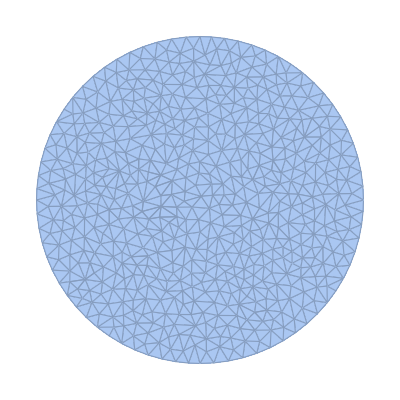

```mathematica
cells0=MeshCells[DR,0];
cells1=MeshCells[DR,1];
cells2=MeshCells[DR,2];
vs=Table[cells0[[i,1]],{i,1,Length[cells0]}];
es=Table[cells1[[i,1]],{i,1,Length[cells1]}];
fs=Table[cells2[[i,1]],{i,1,Length[cells2]}];
ps=MeshCoordinates[DR];
```

```mathematica
SetDirectory["C:\\Users\\jo\\Documents\\Academic Stuff\\Geometría diferencial\\DifferentialGeo_Code\\EcuacionPoisson"]
```

C:\Users\jo\Documents\Academic Stuff\Geometría diferencial\DifferentialGeo_Code\EcuacionPoisson

```mathematica
Export["caras_malla4.txt", fs, "CSV"]
Export["aristas_malla4.txt", es, "CSV"]
Export["coordenadas_malla4.txt", ps, "CSV"]
```

caras_malla4.txt

aristas_malla4.txt

coordenadas_malla4.txt